```mathematica
tauparexp[[1]]
tauparexp[[2]]
tauparexp[[2,1]]
tauparexp[[2,2,1]]
tauparexp[[2,2,2]]
```

(2.51737×10^-24 BrfpG^2 rfp^(2-nu) rmono^nu)/(gamma^2 rp zeta)

6.65077×10^-25 (lmode Lp npairs+(15.1403 BrfpG^2 rfp^(2-nu/2) rmono^(nu/2) Sin[thfp/2])/(gamma r zeta))

6.65077×10^-25

lmode Lp npairs

(15.1403 BrfpG^2 rfp^(2-nu/2) rmono^(nu/2) Sin[thfp/2])/(gamma r zeta)

```mathematica
(15.140290339329972 BrfpG^2 rfp^(2-nu/2) rmono^(nu/2) Sin[thfp/2])/(gamma r zeta)
```

```mathematica
theconsts
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,r→50000000000000,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15}

```mathematica
npairs
```

npairs

```mathematica
solsT
```

{T→(12 c^8 gamma mb me^3 r^2 (rmono/rfp)^(2-nu) (npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)) zeta)/(BrfpG^2 √(1-1/gamma0^2) gamma0 kb π q^4 rmono^2 (Lp npairs Numlayers+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta)) (2 √3+3 sigmat (Lp npairs Numlayers+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta))))}

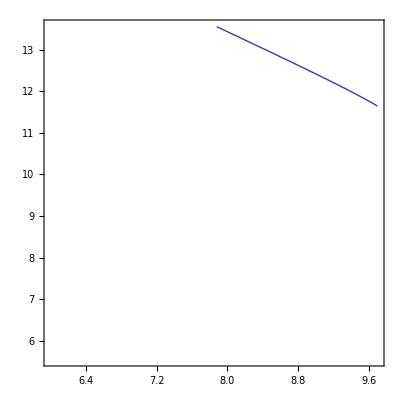

```mathematica
ContourPlot[{pgtouse==pmtouse},{lT,6,Log[10,5*10^9]},{lnpairs,Log[10,0.0001*netouse],Log[10,10000*netouse]}]
```

```mathematica
(* Constants of Nature *)
lowestprec=30;
getconstants:=Module[
{foo},

(* Cabibbo angle *)
(*
s=1;
g=1;
cm=1;
*)

thetac=SetPrecision[13.04*Pi/180,lowestprec];
costhetac=SetPrecision[Cos[thetac],lowestprec];
AU=SetPrecision[149597870.691*10^2,lowestprec];
msun=SetPrecision[1.989*10^(33),lowestprec];
lsun=SetPrecision[3.89*10^(33),lowestprec];
rsun=SetPrecision[695500*10^3*100,lowestprec];
G=SetPrecision[6.672*10^(-8) ,lowestprec];
c=SetPrecision[2.99792458*10^(10) ,lowestprec];
ergPmev=SetPrecision[1.60217649*10^(-6),lowestprec];
h=SetPrecision[4.13566733*10^(-15)*10^(-6)*ergPmev,lowestprec];
hbar=SetPrecision[h/(2*Pi),lowestprec];
mn=SetPrecision[1.674927211*10^(-24),lowestprec];
mp=SetPrecision[1.672621637*10^(-24),lowestprec];
QE=SetPrecision[(mn-mp)*c^2,lowestprec];
me=SetPrecision[9.10938215*10^(-31)*1000,lowestprec];
mealso=SetPrecision[0.510998910*ergPmev/c^2,lowestprec];
(*mb=SetPrecision[(mn+mp)/2,lowestprec];*)
avo=SetPrecision[6.0221367*10^(23),lowestprec];
amu=SetPrecision[1/avo,lowestprec];
mu=SetPrecision[amu,lowestprec];
mb=SetPrecision[mu,lowestprec];
kb=SetPrecision[1.380658*10^(-16),lowestprec]; (* erg/K *)
(*Print["arad"],lowestprec];*)
arad=SetPrecision[8*Pi^5*kb^4/(15*c^3*h^3),lowestprec];
arad=SetPrecision[Pi^2*kb^4/(15*(hbar*c)^3),lowestprec];
sigmasb=SetPrecision[arad*c/4,lowestprec];
q=SetPrecision[4.8029*10^(-10),lowestprec];
secPyr=SetPrecision[(60*60*24*365.25),lowestprec];
Ry=SetPrecision[1.09678*10^5,lowestprec];
RyE=SetPrecision[me*q^4/(2*hbar^2),lowestprec];
fsc=SetPrecision[q^2/(hbar*c),lowestprec];
radiuse=SetPrecision[q^2/(me*c^2),lowestprec];
radiusp=SetPrecision[q^2/(mp*c^2),lowestprec];
alpha=SetPrecision[q^2/(hbar*c),lowestprec];
km=SetPrecision[10^3*100,lowestprec];
pc=SetPrecision[3.086*10^18,lowestprec];
Mpc=SetPrecision[10^6*pc,lowestprec];
rgalaxies=SetPrecision[3*Mpc,lowestprec];
ly=SetPrecision[1/3.261*pc,lowestprec];
h0=SetPrecision[71*km/s/Mpc,lowestprec];
sigmatdiff=SetPrecision[radiuse^2,lowestprec];
sigmat=SetPrecision[(8*Pi/3)*(alpha*hbar/(me*c))^2,lowestprec];
sigmat2=SetPrecision[(8*Pi/3)*(q^4/(me^2*c^4)),lowestprec];
sigmakngen=SetPrecision[(2*Pi*q^4)/(me^2*c^4)*((1+alphakn)/(alphakn^2)*(2*(1+alphakn)/(1+2*alphakn)-1/alphakn*Log[1+2*alphakn])+1/(2*alphakn)*Log[1+2*alphakn]-(1+3*alphakn)/(1+2*alphakn)^2)//.{alphakn->(h*freqgamma)/(me*c^2)},lowestprec];

sigmat-Limit[sigmakn,freqgamma->0];
];
getconstants;
godconsts={BrfpG->1000000000000000,lmode->2,mmode->0,rfp->rl,rl->(3 G msun)/c^2,zeta->10000,gamma->700,rp->r,nu->3/4,rmono->30000000000,thfp->π/2,omegaffp->(0.25 c)/rfp,gamma0->1.15}
super={r->7.6*10^(13),T->3.8*10^8,npairs->3*10^(11),Lptilde->1,Numlayers->1};
myrhob=rhob//.super//.godconsts//.physicalconsts;
myT=T//.super//.godconsts//.physicalconsts;
mybgauss=Sqrt[bsq]//.super//.godconsts//.physicalconsts;
mynpairs=npairs//.super//.godconsts//.physicalconsts;
Pclassgen2[myrhob,myT,mybgauss,mynpairs]//.super//.godconsts//.physicalconsts
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→442966.28205196797014558943382,zeta→10000,gamma→700,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(7.49481×10^9)/rfp,gamma0→1.15}

7.84667×10^6

```mathematica
myomega=omegac[1+kb*myT/(me*c^2),mybgauss]
myomega2=kb*myT/hbar
```

5.69746×10^12

4.97501×10^19

```mathematica
Fsyn[1]
```

0.651423

```mathematica
x
```

x

1/(gamma^2 r^2 zeta)BrfpG^2 rfp^2 (rmono/rfp)^nu (-3.68091×10^-15 gamma √(1-1/gamma0^2) gamma0 T+1.77084×10^-22 etaele omegaffp^2 rfp^2 zeta Sin[thfp/2]^2)

{{zeta→(2.07863×10^7 gamma √(1.-1./gamma0^2) gamma0 T Csc[0.5 thfp]^2)/(etaele omegaffp^2 rfp^2)}}

(4.81087×10^-8 etaele omegaffp^2 rfp^2 zeta Sin[0.5 thfp]^2)/(gamma √(1.-1./gamma0^2) gamma0)

```mathematica
NIntegrate[BesselK[5/3,x],{x,1,Infinity}]
```

0.651423

```mathematica
BesselK[5/3,myomega]
```

General::unfl: Underflow occurred in computation.

Indeterminate

```mathematica
Fsyn[myomega/omegac[1,mybgauss]]
```

0.651423

```mathematica
Tobsconsts2
```

{gamma→gamma,gammaesyn→1/(√((c^4 gamma^2 (-1+gamma0^2) me^2)/(c^2 gamma √(1-1/gamma0^2) gamma0 me+3 etaele mb omegaffp^2 rfp^2 zeta-3 etaele mb omegaffp^2 rfp^2 zeta Cos[thfp])^2)),(4 BrfpG^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(c^2 gamma^2 r^2)→(4 BrfpG^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(c^2 gamma^2 r^2),etaele→0.1}

```mathematica
FullSimplify[Epeakobskevinj,{gamma>0,BrfpG>0,rfp>0,rmono>0,etaele>0,zeta>0,thfp>0,c>0,ergPmev>0,me>0,r>0,mb>0,omegaffp>0,gamma0>0}]
```

(870. BrfpG hbar omegaffp q √(rfp^(4-nu) rmono^nu) Abs[Sin[thfp/2]] (c^2 gamma √(-1+gamma0^2) me+3. etaele mb omegaffp^2 rfp^2 zeta-3. etaele mb omegaffp^2 rfp^2 zeta Cos[thfp])^2)/(c^6 ergPmev gamma^2 (-1.+gamma0^2) me^3 r)

```mathematica
(1+(601.8619409116859 etaele zeta)/gamma-(601.8619409116859 etaele zeta Cos[thfp])/gamma)
```

```mathematica
(1+(859.8027727309799 etaeletilde zetatilde (1-Cos[thfp]))/gammatilde)//.{zetatilde->14*gammatilde}
```

1+12037.2 etaeletilde (1-Cos[thfp])

```mathematica
integrand[myrhob,1+kb*myT/(me*c^2),myT,mynpairs,myomega,mybgauss]
```

0.000017138

```mathematica
Pofomega[myrhob,myT,mybgauss,mynpairs,myomega2]
```

$Aborted

$Aborted

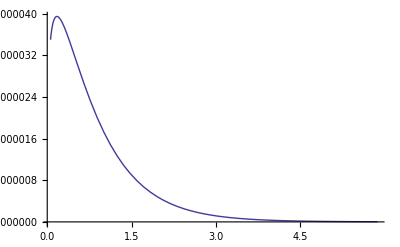

```mathematica
Plot[Pofomega[myrhob,myT,mybgauss,mynpairs,omega],{omega,myomega/10,myomega*10}]
```

```mathematica
{{2.013*^12,3.934*^-6}}
```

$Aborted

```mathematica
2.013*10^(12)/myomega
```

0.353315

```mathematica
Fsyn[1]
```

0.651423

```mathematica
myomega=omegac[1.08,mybgauss]
myomega2=kb*myT/hbar
```

5.86919×10^12

4.97501×10^19

```mathematica
Plot3D[integrand[myrhob,gammap,myT,mynpairs,omega,mybgauss],{omega,0,2*myomega},{gammap,1,2}]
```

$Aborted

```mathematica
Integrate[BesselK[5/3,x],{x,x0,Infinity}]
```

If[x0>0,(2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},x0^2/4])/x0^(2/3)+(π (-320+(81 2^(1/3) x0^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},x0^2/4])/Gamma[-1/3]))/(320 √3),Integrate[BesselK[5/3,x],{x,x0,∞},Assumptions→x0≤0]]

```mathematica
Plot[jclassgen3[1+kb*myT,mybgauss,omegap,mybgauss],{omegap,0,2}]
```

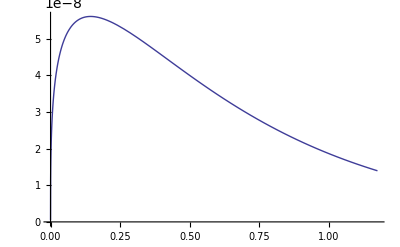

5.86919×10^12

4.97501×10^19

```mathematica
Plot[integrand[myrhob,1+kb*myT,myT,mynpairs,omegap,mybgauss],{omegap,0,2*myomega}]
```

```mathematica
omegap
```

omegap

```mathematica
omega
```

omega

```mathematica
Fsyn[1.]
```

0.651423

```mathematica
Pofomega[myrhob,myT,mybgauss,mynpairs,myomega]
```

Pofomega[myrhob,myT,mybgauss,mynpairs,myomega]

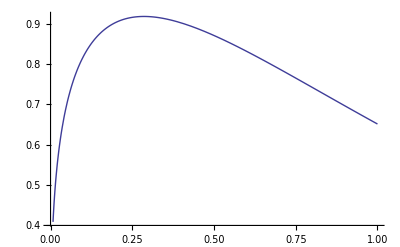

```mathematica
Plot[Fsyn[x],{x,0,1}]
```

```mathematica
Pofomega[1,me*c^2/kb,1,1,1]
```

NIntegrate::inum: Integrand BesselK[5/3, x] is not numerical at {x} = {124.67045260960337`  + omegap}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::inumr: The integrand 7.289806313377608`28.1755832945061*^18 ⅇ^-1.`15.954589770191005 gammap$42830 √1 - 1/gammap$42830^2 gammap$42830^5 omegap NIntegrate[BesselK[5/3, x], {x, omegap, ∞}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 1.`}}.

NIntegrate[integrand[1,gammap$42830,5.9298569105493378141132490384×10^9,1,1,1],{gammap$42830,1,∞}]

```mathematica
10^11.673
```

4.70977×10^11

```mathematica
fit//.super//.godconsts//.physicalconsts
npairsfunc//.super//.godconsts//.physicalconsts
(upairs/(kb*T))//.super//.godconsts//.physicalconsts
```

0.0792161

7.36943×10^8

9.30295×10^9

```mathematica
pg//.super//.godconsts//.physicalconsts

gtau//.super//.godconsts//.physicalconsts
(3*tautot+2*Sqrt[3])/(3*tautot+2*Sqrt[3]+2/tauabs)//.super//.godconsts//.physicalconsts
htau//.super//.godconsts//.physicalconsts

Qsnonrel2//.super//.godconsts//.physicalconsts
Qs2//.super//.godconsts//.physicalconsts
```

5.56477×10^8

1.05821×10^-11

1.05821×10^-11

3.82422×10^-12

7.91836×10^6

8.29893×10^6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 1.52219×10^-43 and 1.33933×10^-47 for the integral and error estimates.

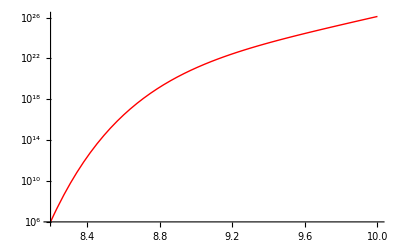

```mathematica
p1=LogPlot[upairsfull[10^lT],{lT,8.2,10},PlotStyle->{Red}]
```

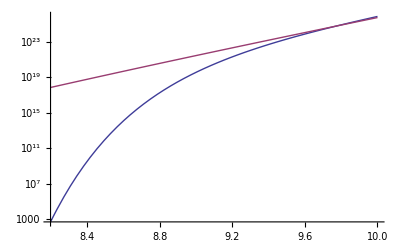

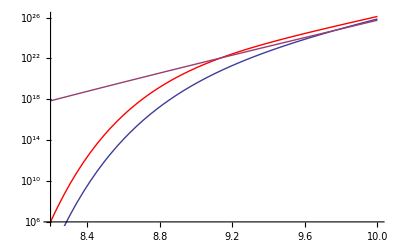

```mathematica
toplot1=Exp[-me*c^2/(1*kb*T)]*urad0*(7/4)//.{T->10^lT};
toplot=Exp[-(me*c^2/(kb*T))^(1/4)]*urad0*(7/4)//.{T->10^lT};
p2=LogPlot[{toplot1,toplot},{lT,8.2,10}]
Show[{p1,p2}]
```

```mathematica
npairsfull[myT,myrhob]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 2.09409×10^-27 and 7.03929×10^-30 for the integral and error estimates.

1.34288×10^22

```mathematica
npairsfull[myT,myrhob]*gtau//.super//.godconsts//.physicalconsts
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 2.09409×10^-27 and 7.03929×10^-30 for the integral and error estimates.

1.42104×10^11

```mathematica
(upairsfull[myT]/(17*kb*myT))
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 1.89164×10^-33 and 7.43825×10^-36 for the integral and error estimates.

1.36007×10^22

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 2.76814×10^-47 and 1.30574×10^-50 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 2.32483×10^-53 and 1.11748×10^-56 for the integral and error estimates.

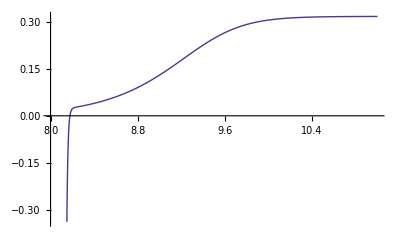

```mathematica
p1=Plot[npairsfull[10^lT,myrhob]/((upairsfull[10^lT]/(kb*10^lT))),{lT,8,11}]
```

```mathematica
myT
```

3.8×10^8

```mathematica
theconsts
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,r→7.6×10^13,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15}

```mathematica
npairsfull[5*10^8,10^(-8)]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 1.38546×10^-25 and 5.1646×10^-28 for the integral and error estimates.

8.88452×10^23

```mathematica
ne//.theconsts//.physicalconsts
rhob//.theconsts//.physicalconsts
```

1.54235×10^11

5.12227×10^-13

```mathematica
npairsfunc[3.8*10^8,3*10^(11)]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 2.09409×10^-27 and 7.03929×10^-30 for the integral and error estimates.

1.42104×10^11

```mathematica
10^(11.8)
```

6.30957×10^11

```mathematica
npairsfunc[10^lT,10^lnpairs]
```

```mathematica
theconstsfull
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,r→7.6×10^13,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15,npairs→2.9×10^11,Lptilde→1,Numlayers→1}

```mathematica
up={{10.01,0.3006}}
down={{8.196,0.01981}}
slope=(up[[1,2]]-down[[1,2]])/(up[[1,1]]-down[[1,1]])
fit=down[[1,2]] + slope*(lT-down[[1,1]]);
```

{{10.01,0.3006}}

{{8.196,0.01981}}

0.154791

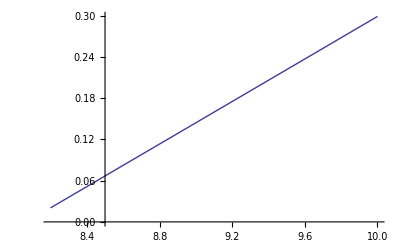

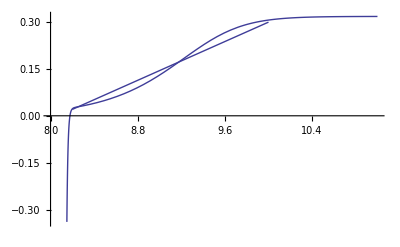

```mathematica
p2=Plot[fit,{lT,8.2,10.0}]
Show[{p1,p2}]
```

```mathematica
myT
```

3.8×10^8

```mathematica
getconstants
```

```mathematica
Clear[Eperparticle]
```

```mathematica
Eperparticle[10^(-8),10^8,10^5,0]/kb
```

6.08297×10^9

```mathematica
Eperparticle=-me*c^2+Epart[10^(-8),10^8,10^5,0]/Npart[10^(-8),10^8,10^5,0]
```

2.11391×10^-8

```mathematica
Eperparticle/(kb*T)//.{T->10^8}
```

1.53109

```mathematica
thetae=(kb*T)/(me*c^2)
Thetae=(3/2)*thetae
ve=c*Sqrt[Thetae*(2+Thetae)]/(1+Thetae)
venonrel=c*Sqrt[3*kb*T/(me*c^2)]
gammae=1/Sqrt[1-(ve/c)^2]
gammaultra=Sqrt[2]*Thetae
```

1.686381332778838834559649613×10^-10 T

2.5295719991682582518394744195×10^-10 T

(476808.75980209477142654938558 √((2+2.5295719991682582518394744195×10^-10 T) T))/(1+2.5295719991682582518394744195×10^-10 T)

674309.41477041784926815145354 √T

1/(√(1-(2.5295719991682582518394744195×10^-10 (2+2.5295719991682582518394744195×10^-10 T) T)/((1+2.5295719991682582518394744195×10^-10 T)^2)))

3.5773550282229743281468627924×10^-10 T

```mathematica
pe=gammae*ve*me//.{T->10^8}
Ee=(Sqrt[pe^2*c^2+me^2*c^4]-me*c^2)//.{T->10^8}
```

6.1812650971394227567473767345×10^-18

2.07098699999999977930239387×10^-8

```mathematica
(* for testing synch power vs. simple power and per-particle energy vs. estimate *)
ne4[rhob_]:=rhob/mb*Ye;
netot4[rhob_,npairs_]:=ne4[rhob]+npairs;
Thetadep2[T_]:=(kb*T)/(me*c^2);
beta2[gamma_]:=Sqrt[1-1/gamma^2];
fgamfullfree2[T_]:=1/(Thetadep2[T]*BesselK[2,1/Thetadep2[T]]);
fgamfullfixedT2[gamma_,T_]:=gamma^2*beta2[gamma]*Exp[-gamma/Thetadep2[T]];
jclassgen2[gamma_,bgauss_]:=2*q^4*bgauss^2*(gamma^2-1)/(3*me^2*c^3);
pitchpart=Integrate[Sin[th]^3,{th,0,Pi}]; (* emissivity has Sin[thetap]^2 and then assume isotropic, so density weight is Sin[thetap]d\thetap *)
Pclassgen2[rhob_,T_,bgauss_,npairs_]:=Module[{omegap,gammap},netot4[rhob,npairs]*fgamfullfree2[T]*NIntegrate[pitchpart*fgamfullfixedT2[gammap,T]*jclassgen2[gammap,bgauss],{gammap,1,Infinity}]];
pmom[gam_]:=Sqrt[gam^2-1]*me*c
Eele[gam_]:=Sqrt[pmom[gam]^2*c^2+me^2*c^4]
Npart[rhob_,T_,bgauss_,npairs_]:=Module[{omegap,gammap},fgamfullfree2[T]*NIntegrate[pitchpart*fgamfullfixedT2[gammap,T],{gammap,1,Infinity}]];
Epart[rhob_,T_,bgauss_,npairs_]:=Module[{omegap,gammap},fgamfullfree2[T]*NIntegrate[Eele[gammap]*pitchpart*fgamfullfixedT2[gammap,T],{gammap,1,Infinity}]];
Eperparticle[rhob_,T_,bgauss_,npairs_]:=Epart[rhob,T,bgauss,npairs]/Npart[rhob,T,bgauss,npairs];
```

```mathematica
rat
```

c/(8 √2 π √((q^2 (npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)))/mb) √((BrfpG^2 c^2 Lptilde mb^2 omegaffp^2 r rfp^2 rmono^2 (rmono/rfp)^(-2+(3 nu)/2) sigmat zeta^2 Sin[thfp/2]^2 (Lptilde npairs Numlayers π r (rmono/rfp)^(-nu/2) Sin[thfp/2]+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta)) (2 √3+3 sigmat (Lptilde npairs Numlayers π r (rmono/rfp)^(-nu/2) Sin[thfp/2]+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta))))/(q^2 (npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)) (BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) rfp^2 (rmono/rfp)^nu+8 c^2 gamma Lptilde mb npairs Numlayers π^2 r^2 zeta) (16 √3 c^2 gamma mb π r (rmono/rfp)^(nu/2) zeta+3 BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) rfp^2 (rmono/rfp)^nu sigmat Sin[thfp/2]+24 c^2 gamma Lptilde mb npairs Numlayers π^2 r^2 sigmat zeta Sin[thfp/2]))))

```mathematica
pgtouse
```

1.03736 2^(-2+lT) 5^lT

```mathematica
Solve[pgtouse==pmtouse,lT]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{lT→9.74678}}

```mathematica
10^(11.87)
```

7.4131×10^11

```mathematica
7.4*10^(11)/(ne//.theconsts//.physicalconsts)
```

4.79787

```mathematica
rat;
solsrat=Solve[PowerExpand[rat]==1,r]
```

$Aborted

```mathematica
rat
```

c/(4 √(2 π) √((BrfpG^2 √(1-1/gamma0^2) gamma0 q^2 rmono^2 (rmono/rfp)^(-2+nu))/(c^2 gamma mb^2 r^2 zeta)) √((c^2 Lptilde mb^2 omegaffp^2 r^2 rfp^2 (rmono/rfp)^(-nu/2) sigmat zeta^2 Sin[thfp/2]^3 (2 √3+(3 BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) sigmat Sin[thfp/2])/(8 c^2 gamma mb π r zeta)))/(gamma0 √((-1+gamma0^2)/gamma0^2) q^2 (16 √3 c^2 gamma mb π r zeta+3 BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) rfp^2 (rmono/rfp)^(nu/2) sigmat Sin[thfp/2]))))

```mathematica
solsT//.physicalconsts
```

{T→(7.98571×10^30 gamma^2 r^2 (rmono/rfp)^(-nu/2) zeta^2 Csc[thfp/2])/(BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) rfp^2 (0.129934 gamma r zeta+1.99523×10^-24 BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) rfp^2 (rmono/rfp)^(nu/2) Sin[thfp/2]))}

```mathematica
etag
```

1/(3 c^7 gamma^2 me^3 r)4 BrfpG^2 kb omegaffp^2 q^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu/2) sigmat T Sin[thfp/2]^3 (2 √3+(3 BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) sigmat Sin[thfp/2])/(8 c^2 gamma mb π r zeta))

```mathematica
deltasp//.physicalconsts
```

4.24142×10^-31 √(1/gamma^2 BrfpG^2 Lptilde omegaffp^2 rfp^4 T Sin[thfp/2]^4 (2 √3+(5.3194×10^-23 BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(gamma r zeta)))

```mathematica
3*tausca//.theconsts//.physicalconsts
2.*Sqrt[3]
```

0.510474

3.4641

```mathematica
2/3*Sqrt[3.]
```

1.1547

```mathematica
theconsts
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,r→7.6×10^13,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15}

```mathematica
10000/700.
```

14.2857

```mathematica
theconstsfull
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,r→7.6×10^13,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15,npairs→2.9×10^11,Lptilde→1,Numlayers→1}

```mathematica
theconstsfull
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,r→7.6×10^13,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15,npairs→2.×10^11,Lptilde→1,Numlayers→1}

```mathematica
ne//.theconstsfull//.physicalconsts
```

8.90862×10^10

```mathematica
theconstsfull
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15,Lptilde→1,1→1,r→100000000000000,npairs→(7 BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)}

```mathematica
myT
```

(3 c^6 me^3 (rmono/rfp)^nu Csc[thfp/2])/(4 kb Lptilde npairs π^3 q^4 r (2 √3 (rmono/rfp)^(nu/2)+3 Lptilde npairs π r sigmat Sin[thfp/2]))

```mathematica
theconsts
```

Join::heads: Heads List and Rule at positions 1 and 2 are expected to be the same.

Join[{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15},r→200000000000000]

```mathematica
theconstsfullnor
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15,npairs→(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta),Lptilde→1,1→1}

```mathematica
myr-(myr//.{r->0})
```

0

```mathematica
physicalconsts
```

{msun→1.989×10^33,G→6.672×10^-8,c→2.99792×10^10,avo→6.02214×10^23,q→4.8029×10^-10,kb→1.38066×10^-16,ergPmev→1.60218×10^-6,h→4.13567×10^-21 ergPmev,hbar→h/(2 π),amu→1/avo,mb→amu,me→9.10938×10^-28,sigmat→(8 π q^4)/(3 c^4 me^2),re→q^2/(c^2 me),arad→(kb^4 π^2)/(15 c^3 hbar^3)}

```mathematica
simpleconsts
```

{mygamma0→1.15,myomegaffp→(0.25 c)/rfp}

```mathematica
myr//.theconstsfullnor//.physicalconsts
```

100728./((1/r^2)^(1/3))

```mathematica
rl
```

rl